```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
Subscript[Ω, m0]=0.315;  H02=(67.37)^2; Subscript[Ω, Λ0]= 0.6847; Subscript[Ω, r0]=  3 10^(-4); H0=Sqrt[H02];
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
Friedmann= (1+z)(β/2) y'[z] - α y[z]  + (  y[z] -Subscript[Ω, m0] H02(1+z)^3 -Subscript[Ω, r0] H02(1+z)^4  )^(2/(2-Δ)) ==0
```

-α y[z]+(-1429.7 (1+z)^3-1.36162 (1+z)^4+y[z])^(2/(2-Δ))+1/2 (1+z) β y'[z]==0

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
Hubbledata=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_H.dat"] //TableForm ;
```

```mathematica
zexp=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_H.dat",{"Table","Data",All,1}][[2;;-1]];
```

```mathematica
Hexp=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_H.dat",{"Table","Data",All,2}][[2;;-1]];
```

```mathematica
Sigexp=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_H.dat",{"Table","Data",All,3}][[2;;-1]];
```

------------------------//-------------------------------------------------//-------------------------------------------------------------//---------------------------------------------------------//--------------------------------

```mathematica
HΛCDM[z_]:= Sqrt[H02(Subscript[Ω, m0](1+z)^3 + Subscript[Ω, r0](1+z)^4  + Subscript[Ω, Λ0])];
```

```mathematica
H[zH_,alpha_,beta_,Delta_]:=Sqrt[NDSolveValue[{Friedmann, y[0]==H02}/. {α-> alpha,β-> beta,Δ-> Delta } ,y[z],{z,zH},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10][[0]][zH]];
```

```mathematica
Dataerror=Table[{ Around[zexp[[i]],0],Around[Hexp[[i]],Sigexp[[i]] ] },{i,1,36}];
```

```mathematica
plotHData=ListPlot[Dataerror,IntervalMarkers->"Fences",IntervalMarkersStyle->Black,PlotLegends-> Placed [{"Datos H(z)"},{0.8,0.4}],PlotStyle->Red];
```

```mathematica
plotHbest=ListLinePlot[Transpose[{zexp,H[zexp,1.0,0.69,0.0]}],PlotStyle->{Dashed,Black},PlotLegends->Placed[ {"Mejor ajuste"},{0.82,0.1}]];
```

```mathematica
LCDM=ListLinePlot[Transpose[{zexp,HΛCDM[zexp]}],PlotStyle->{Blue},PlotLegends-> Placed[{"ΛCDM"},{0.78,0.2}]] ;
```

```mathematica
beta1s=Table[{ Around[zexp[[i]],0],Around[ H[zexp[[i]],1.0,0.69,0.0],{Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0,0.69-0.023,0.0]] , Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0,0.69+0.030,0.0]]} ] },{i,1,36}];
```

```mathematica
legenditemsbeta1s=MapThread[ListLinePlot[Table[{x,Around[1,0.5]},{x,0,1,0.1}],IntervalMarkers->"Bands",PlotStyle-> Directive["LineOpacity"->0],IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.5,Blue]]],AspectRatio->1,Axes->False]&,{ColorData[97]/@{1},{Blue}}];
```

```mathematica
plotbeta1s=ListLinePlot[beta1s,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.5,Blue]]],ImageSize->Large,PlotLegends->Placed[LineLegend[{"1σ(β)"},"LegendItem"->legenditemsbeta1s,LegendMarkerSize->{30,30}],{0.8,0.2}],PlotStyle->Directive["LineOpacity"->0]] ;
```

```mathematica
beta3s=Table[{ Around[zexp[[i]],0],Around[ H[zexp[[i]],1.0,0.69,0.0],{Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0,0.69-0.13,0.0]] , Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0,0.69+0.09,0.0]]} ] },{i,1,36}];
```

```mathematica
legenditemsbeta3s=MapThread[ListLinePlot[Table[{x,Around[1,0.5]},{x,0,1,0.1}],IntervalMarkers->"Bands",PlotStyle->Directive["LineOpacity"->0],IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.25,Blue]]],AspectRatio->1,Axes->False]&,{ColorData[97]/@{1},{Blue}}];
```

```mathematica
plotbeta3s=ListLinePlot[beta3s,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.25,Blue]]],ImageSize->Large,PlotLegends->Placed[LineLegend[{"3σ(β)"},"LegendItem"->legenditemsbeta3s,LegendMarkerSize->{30,30}],{0.8,0.3}],PlotStyle->Directive["LineOpacity"->0]] ;
```

```mathematica
alpha1s=Table[{ Around[zexp[[i]],0],Around[ H[zexp[[i]],1.0,0.69,0.0],{Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0-0.018,0.69,0.0]] , Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0+0.018,0.69,0.0]]} ] },{i,1,36}];
```

```mathematica
legenditemsalpha1s=MapThread[ListLinePlot[Table[{x,Around[1,0.5]},{x,0,1,0.1}],IntervalMarkers->"Bands",PlotStyle-> Directive["LineOpacity"->0],IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.65,Purple]]],AspectRatio->1,Axes->False]&,{ColorData[97]/@{1},{Green}}] ;
```

```mathematica
plotalpha1s=ListLinePlot[alpha1s,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive["LineOpacity"->0,Thickness[5],FaceForm[Opacity[.65,Purple]]],ImageSize->Large,PlotLegends->Placed[LineLegend[{"1σ(α)"},"LegendItem"->legenditemsalpha1s,LegendMarkerSize->{30,30}],{0.8,0.2}],PlotStyle->Directive["LineOpacity"->0]];
```

```mathematica
alpha3s=Table[{ Around[zexp[[i]],0],Around[ H[zexp[[i]],1.0,0.69,0.0],{Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0-0.11,0.69,0.0]] , Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0+0.11,0.69,0.0]]} ] },{i,1,36}];
```

```mathematica
legenditemsalpha3s=MapThread[ListLinePlot[Table[{x,Around[1,0.5]},{x,0,1,0.1}],IntervalMarkers->"Bands",PlotStyle->Directive["LineOpacity"->0],IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.25,Purple]]],AspectRatio->1,Axes->False]&,{ColorData[97]/@{1},{Purple}}] ;
```

```mathematica
plotalpha3s=ListLinePlot[alpha3s,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.25,Purple]]],ImageSize->Large,PlotLegends->Placed[LineLegend[{"3σ(α)"},"LegendItem"->legenditemsalpha3s,LegendMarkerSize->{30,30}],{0.8,0.3}],PlotStyle->Directive["LineOpacity"->0]]  ;
```

```mathematica
delta1s=Table[{ Around[zexp[[i]],0],Around[ H[zexp[[i]],1.0,0.69,0.0],{Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0,0.69,0.0-0.004]] , Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0,0.69,0.0+0.004]]} ] },{i,1,36}];
```

```mathematica
legenditemsdelta1s=MapThread[ListLinePlot[Table[{x,Around[1,0.5]},{x,0,1,0.1}],IntervalMarkers->"Bands",PlotStyle-> Directive["LineOpacity"->0],IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.5,Orange]]],AspectRatio->1,Axes->False]&,{ColorData[97]/@{1},{Orange}}]  ;
```

```mathematica
plotdelta1s=ListLinePlot[delta1s,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.5,Orange]]],ImageSize->Large,PlotLegends->LineLegend[{"1σ(Δ)"},"LegendItem"->legenditemsdelta1s,LegendMarkerSize->{30,30}],PlotStyle->Directive["LineOpacity"->0]];
```

```mathematica
delta3s=Table[{ Around[zexp[[i]],0],Around[ H[zexp[[i]],1.0,0.69,0.0],{Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0,0.69,0.0-0.030]] , Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0,0.69,0.0+0.030]]} ] },{i,1,36}] ;
```

```mathematica
legenditemsdelta3s=MapThread[ListLinePlot[Table[{x,Around[1,0.5]},{x,0,1,0.1}],IntervalMarkers->"Bands",PlotStyle->Directive["LineOpacity"->0],IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.25,Orange]]],AspectRatio->1,Axes->False]&,{ColorData[97]/@{1},{Orange}}];
```

```mathematica
plotdelta3s=ListLinePlot[delta3s,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.25,Orange]]],ImageSize->Large,PlotLegends->LineLegend[{"3σ(Δ)"},"LegendItem"->legenditemsdelta3s,LegendMarkerSize->{30,30}],PlotStyle->Directive["LineOpacity"->0]]  ;
```

```mathematica
sigma3s=Table[{ Around[zexp[[i]],0],Around[ H[zexp[[i]],1.0,0.69,0.0],{Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0-0.11,0.69-0.13,0.0-0.030]] , Abs[H[zexp[[i]],1.0,0.69,0.0] - H[zexp[[i]],1.0+0.11,0.69+0.09,0.0+0.030]]} ] },{i,1,36}] ;
```

```mathematica
legenditemssigma3s=MapThread[ListLinePlot[Table[{x,Around[1,0.5]},{x,0,1,0.1}],IntervalMarkers->"Bands",PlotStyle->Directive["LineOpacity"->0],IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.5,Orange]]],AspectRatio->1,Axes->False]&,{ColorData[97]/@{1},{Orange}}];
```

```mathematica
plotsigma3s=ListLinePlot[sigma3s,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.5,Orange]]],ImageSize->Large,PlotLegends->Placed[LineLegend[{"3σ(α,β,Δ)"},"LegendItem"->legenditemssigma3s,LegendMarkerSize->{30,30}],{0.8,0.3}],PlotStyle->Directive["LineOpacity"->0]];
```

```mathematica
Show[plotHData,plotbeta3s,plotbeta1s,plotHbest,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"H(z)",""},{z,"α = 1.0 , β = 0.69 , Δ = 0.0"}}]
```

-Graphics-

```mathematica
Show[plotHData,plotalpha3s,plotalpha1s,plotHbest,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"H(z)",""},{z,"α = 1.0 , β = 0.69 , Δ = 0.0"}}]
```

-Graphics-

```mathematica
Show[plotHData,plotsigma3s,LCDM,plotHbest,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"H(z)",""},{z,"α = 1.0 , β = 0.69 , Δ = 0.0"}}]
```

-Graphics-

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
H2[Z_,alpha_,beta_,Delta_]:=NDSolveValue[{Friedmann, y[0]==H02}/. {α-> alpha,β-> beta,Δ-> Delta} ,y[z],{z,0.0,Z},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->40,PrecisionGoal->10][[0]]
```

```mathematica
dL[Z_,alp_,bet_,Delt_]:= (1+Z)*NIntegrate[1/Sqrt[Evaluate[H2[Z,alp,bet,Delt][x]]],{x,0.0,Z},Method->"LocalAdaptive"]
```

```mathematica
mb[Z_,alpha_,beta_,Delta_,M_]:= -M + 5*Log10[dL[Z,alpha,beta,Delta]]-5*Log10[H0] + 25
```

```mathematica
mb[2.25,0.99,0.1,0.0,-17.8]
```

26.283

```mathematica
SNa1data=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_SNa1_Obs.txt"] //TableForm ;
```

```mathematica
zexpSN=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_SNa1_Obs.txt",{"Table","Data",All,2}][[2;;-1]];
```

```mathematica
mbexp=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_SNa1_Obs.txt",{"Table","Data",All,5}][[2;;-1]];
```

```mathematica
Sigmb=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/data_SNa1_Obs.txt",{"Table","Data",All,6}][[2;;-1]];
```

```mathematica
tablam=Table[{ zexpSN[[i]],mb[zexpSN[[i]],1.,0.69,0.0,-17.097]},{i,1,Dimensions[zexpSN][[1]]}] ;
```

```mathematica
tablam1sigmaup=Table[{ zexpSN[[i]],mb[zexpSN[[i]],1.,0.69,0.0,-17.097+0.013]},{i,1,Dimensions[zexpSN][[1]]}] ;
```

```mathematica
tablam1sigmadown=Table[{ zexpSN[[i]],mb[zexpSN[[i]],1.,0.69,0.0,-17.097-0.012]},{i,1,Dimensions[zexpSN][[1]]}] ;
```

```mathematica
tabla2=TableForm[Prepend[Partition[Flatten[tablam],2],{"  z","mb"}]];
```

```mathematica
tabla1sup=TableForm[Prepend[Partition[Flatten[tablam1sigmaup],2],{"  z","mb"}]];
```

```mathematica
tabla1sdown=TableForm[Prepend[Partition[Flatten[tablam1sigmadown],2],{"  z","mb"}]];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO

```mathematica
Export["mb.csv",tabla2,"FieldSeparators"->"        "]; Export["mb1sup.csv",tabla1sup,"FieldSeparators"->"        "]; Export["mb1sdown.csv",tabla1sdown,"FieldSeparators"->"        "];
```

```mathematica
tablamb=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/mb_py.csv"] ;
```

```mathematica
tablamb1sup=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/mb1sup_py.csv"] ;
```

```mathematica
tablamb1sdown=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/mb1sdown_py.csv"] ;
```

```mathematica
pm1=ListLinePlot[tablamb,PlotLegends->Placed[{"Mejor ajuste"},{0.8,0.15}],PlotStyle->{Black,Thickness[0.0035]},ScalingFunctions->{"Log"}];
```

```mathematica
tablamb1sigma=Table[{ Around[tablamb[[i]][[1]],0],Around[ tablamb[[i]][[2]],{Abs[tablamb[[i]][[2]] - tablamb1sdown[[i]][[2]]] , Abs[tablamb[[i]][[2]] - tablamb1sup[[i]][[2]]]} ] },{i,1,1048}];
```

```mathematica
Dataerrormb=Table[{ Around[zexpSN[[i]],0],Around[mbexp[[i]],Sigmb[[i]] ] },{i,1,Dimensions[zexpSN][[1]]}];
```

```mathematica
pmd=ListPlot[Dataerrormb,IntervalMarkers->"Fences",IntervalMarkersStyle->Directive[Darker[Hue[0.4,0.9]],Thin,FaceForm[Opacity[1.2]]],PlotRange->All,PlotStyle->Red,PlotLegends->Placed[{"Datos SNa1"},{0.8,0.35}],ScalingFunctions->{"Log"}]  ;
```

```mathematica
legenditemM3s=MapThread[ListLinePlot[Table[{x,Around[1,0.5]},{x,0,1,0.1}],IntervalMarkers->"Bands",PlotStyle->Directive["LineOpacity"->0],IntervalMarkersStyle->Directive["LineOpacity"->0,FaceForm[Opacity[.65,Blue]]],AspectRatio->1,Axes->False]&,{ColorData[97]/@{1},{Blue}}];
```

```mathematica
pmd1s=ListLinePlot[tablamb1sigma,IntervalMarkers->"Bands",IntervalMarkersStyle->Directive[Thickness[0.01],FaceForm[Opacity[.5,Blue]]],PlotLegends->Placed[LineLegend[{"3σ(M)"},"LegendItem"->legenditemM3s,LegendMarkerSize->{30,30}],{0.775,0.25}],PlotStyle->Opacity[.35,Blue],ScalingFunctions->{"Log"}] ;
```

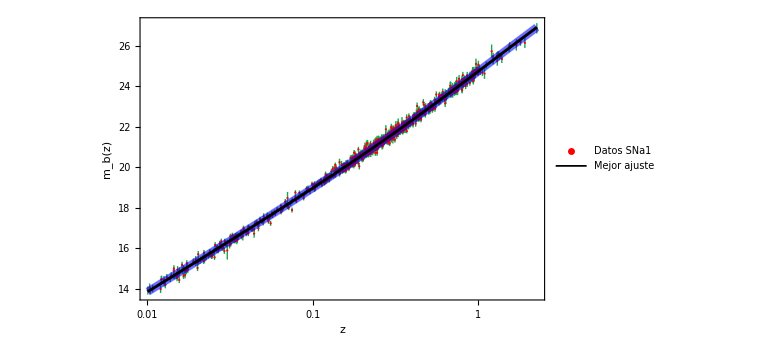

```mathematica
Show[pmd,pmd1s,pm1,PlotRange-> All,LabelStyle->Directive[Black,Bold,10],ImageSize->Large,Frame->True, FrameLabel->{{"m_b(z)",""},{z,"α = 1.0 , β = 0.69 , Δ = 0.0 , M = -17.097"}}]
```

```mathematica
Chi[mEXP_,mTEO_,SigEXP_]:= N[(mEXP-mTEO)^(2) / (SigEXP)^2 ];
```

```mathematica
Chi2[M_]:=  Sum[  Chi[mbexp[[i]],   N[Re[ mb[zexpSN[[i]],1.,0.69,0.0,M]]],Sigmb[[i]]],{i,1,1048}];
```

```mathematica
Dimensions[Range[-21,-16,0.06]]
```

{84}

```mathematica
tabla=Table[{ NumberForm[M,{4,4}],Chi2[M]},{M,-21,-16,0.06}]
```

```mathematica
data=TableForm[Prepend[Partition[Flatten[tabla],2],{"   M","Χ.b2(M)"}]];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO

```mathematica
Export["chiM.csv",data,"FieldSeparators"->"        "];
```

```mathematica
dataM=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/chiM.dat"][[2;;-1]] //TableForm ;
```

```mathematica
Mchi=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/chiM.dat",{"Table","Data",All,2}][[2;;-1]];
```

```mathematica
MinMax[Mchi]
```

{1082.09,903590.}

```mathematica
Position[Mchi,_?(#==Min[Mchi]&)][[1]]
```

{67}

```mathematica
MinParameteres=Extract[dataM,{1,67}]
```

{-17.04,1082.09}

```mathematica
MinParameteres[[2]]
```

1082.09

```mathematica
Mpy=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/M_py.csv"] ;
```

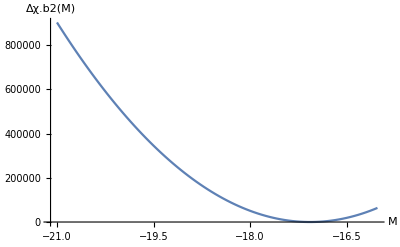

```mathematica
ListLinePlot[Mpy,AxesLabel->{"M","Δχ.b2(M)"},LabelStyle->Directive[Black,Bold,10],AxesOrigin->{-21.1,0.0}]
```

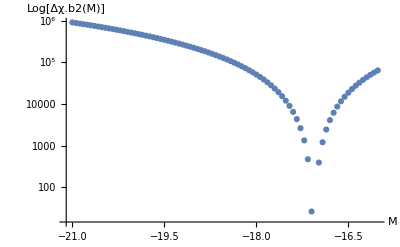

```mathematica
ListLogPlot[Mpy,AxesLabel->{"M","Log[Δχ.b2(M)]"},LabelStyle->Directive[Black,Bold,10],AxesOrigin->{-21.1,0.0}]
```

```mathematica
Mrango=Range[-17.15,-17.05,0.0012] ;
```

```mathematica
tabla2=Table[{ NumberForm[M,{6,3}],Chi2[M]},{M,Mrango}];
```

```mathematica
data2=TableForm[Prepend[Partition[Flatten[tabla2],2],{"   M","Χ.b2(M)"}]];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO

```mathematica
Export["chi2M_big.csv",data2,"FieldSeparators"->"        "];
```

```mathematica
M2py=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/M2_py.csv"] ;
```

```mathematica
Export["chi2M_big.dat",data2,"FieldSeparators"->"        "];
```

```mathematica
M2chi=Import["/home/miguel/Documentos/Wolfram Mathematica/HDE_Barrow_GO/chi2M_big.dat",{"Table","Data",All,2}][[2;;-1]];
```

```mathematica
MinMax[M2chi]
```

{1038.22,1203.85}

```mathematica
Position[M2chi,_?(#==Min[M2chi]&)][[1]]
```

{45}

```mathematica
MinParameteres=Extract[data2,{1,45+1}]
```

{-17.097,1038.22}

```mathematica
MinParameteres[[2]]
```

1082.09

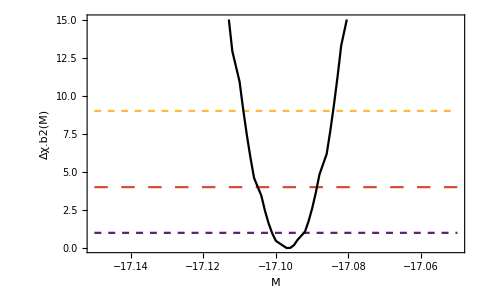

```mathematica
M2plot=ListLinePlot[{{{M2py[[1]][[1]],1.0},{M2py[[-1]][[1]],1.0}},{{M2py[[1]][[1]],4.0},{M2py[[-1]][[1]],4.0}},{{M2py[[1]][[1]],9.0},{M2py[[-1]][[1]],9.0}},M2py},LabelStyle->Directive[Black,Bold,10],Frame->True,FrameLabel->{{Rotate["Δχ.b2(M)",270 Degree],""},{"M",""}},PlotLegends-> Placed[LineLegend[{"68.27% (1σ)","95.45% (2σ)","99.73% (3σ)"},LegendMarkerSize->{15,10},LabelStyle->Directive[FontSize->11]],{0.2,0.725},Rotate[#, 0]&],PlotStyle->{Directive[Dashed,RGBColor["#582078"]],Directive[Dashing[0.02],RGBColor["#d54e37"]],Directive[Dashing[0.01],RGBColor["#ffbb38"]],Black},PlotRange->{0,15}]
```

```mathematica
IntervaloM=Graphics`Mesh`FindIntersections@M2plot
```

{{-17.1089,9.},{-17.105,4.},{-17.1011,1.},{-17.0923,1.},{-17.0887,4.},{-17.0842,9.}}

```mathematica
DeltaMsigma=Around[-17.097,{-17.097-IntervaloM[[3]][[1]], -17.097-IntervaloM[[4]][[1]] }]
```

-17.0970.0040.005

```mathematica
DeltaM2sigma=Around[-17.097,{-17.097-IntervaloM[[2]][[1]], -17.097-IntervaloM[[5]][[1]] }]
```

-17.0970.0080.008

```mathematica
DeltaM3sigma=Around[-17.097,{-17.097-IntervaloM[[1]][[1]], -17.097-IntervaloM[[6]][[1]] }]
```

-17.0970.0120.013